# Components of variability w/ variable transmission

We want to articulate how changing components of temperature vs supply (since we are drawing both from a distribution) change R0 / phi

## Parameters & Helpers

```mathematica
(* ----------------------------------------------------------------------- *)
(* 00  Directory helpers                                                   *)
(* ----------------------------------------------------------------------- *)
Off[General::munfl] 
(* main figure directory (relative to this notebook) *)
figDir = FileNameJoin[{NotebookDirectory[], "..", "..", "figs", "si", 
                       "s-vs-t-variability"}];
If[! DirectoryQ[figDir], 
  CreateDirectory[figDir, CreateIntermediateDirectories -> True]];

(* data directory for binary objects *)
dataDir = FileNameJoin[{NotebookDirectory[], "..", "..", "outputs", 
                        "intermediate-obs", "s-vs-t-variability"}];
If[! DirectoryQ[dataDir], 
  CreateDirectory[dataDir, CreateIntermediateDirectories -> True]];
```

Set the simple things as functions

```mathematica
ClearAll[ImaxFunc, RespirationFunc, SuitabilityFunc, epsFunc, phiLandscape];

ImaxFunc[T_, optT_, respBreadth_] :=
  Exp[-((T - optT)^2)/respBreadth];

RespirationFunc[T_, {ma_, mb_, mc_}] :=
  ma*Exp[mb*T] + mc;

SuitabilityFunc[T_, R_, params_Association] :=
 Module[{imax, m},
   imax = ImaxFunc[T, params["optT"], params["respBreadth"]];
   m = RespirationFunc[T, params["mParams"]];
   Max[0, (imax*R)/(R + params["Rhalf"]) - m]
 ];
(*epsFunc[T_] := 1/(1 + Exp[-0.25 (T - 22)]);*)
epsFunc[T_] := Module[
  {σ = 0.05, μ = Log[28] - 0.05^2/2},
  PDF[LogNormalDistribution[μ, σ], T] /
    PDF[LogNormalDistribution[μ, σ], 28]
];
phiLandscape[meanT_, varT_, meanR_, varR_]:=
  Module[{temps,supp,wRaw,wNorm},
    temps = RandomVariate[NormalDistribution[meanT, varT], nPatches];
    supp  = RandomVariate[NormalDistribution[meanR, varR], nPatches];
    wRaw  = MapThread[SuitabilityFunc[#1,#2,suitParams]&,
                     {temps, supp}];
	 wNorm = With[{s = Total[wRaw]},
	  If[s == 0,
	     ConstantArray[0, Length[wRaw]],  (* all zero if nothing to normalize *)
	     wRaw/s                          (* otherwise the usual normalization *)
	  ]
	];
	(* compute epsilon at each patch temperature *)
    epsVec = epsFunc /@ temps;
    
    Total[ wNorm * (1 - (1 - wNorm*epsVec)^totalS) ]
  ];
```

Show how the transmission curve changes with temperature

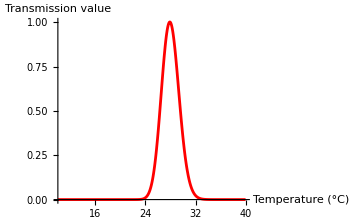

```mathematica
Tmin = 10;  Tmax = 40;

epsCurve = Plot[
  epsFunc[T],
  {T, Tmin, Tmax},
  PlotRange   -> All,
  PlotStyle -> Red,
  AxesLabel   -> {"Temperature (°C)", "Transmission value"},
  PlotLabel   -> "",
  PlotStyle   -> Thick,
  ImageSize   -> Medium
]
```

We’ll start by simulating some situations manually so we can see the results

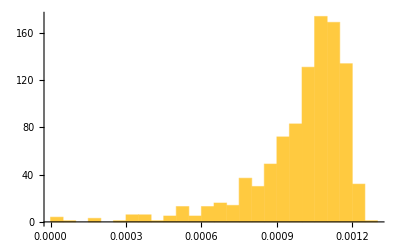

```mathematica
(* constant values for now *)
epsF = 1;
(* suitability-function constants *)
suitParams = <|
  "optT"     -> 25, (* Optimal temperature *)
  "respBreadth"  -> 150, (* Temperature response breadth *)
  "Rhalf"  -> 0.1,
  "mParams"-> {0.05, 0.1, 0.05}
|>;

(* variable things *)
nPatches = 1000;
totalS = 1000;
meanR = 0.8;
meanT = 22;
varR = 0.2;
varT = 2;

(* make a landscape to start with *)
temps = RandomVariate[NormalDistribution[meanT, varT], nPatches];
supp  = RandomVariate[NormalDistribution[meanR, varR], nPatches];
wRaw  = MapThread[SuitabilityFunc[#1, #2, suitParams] &, {temps, supp}];
wNorm = wRaw/Total[wRaw]; (* ensure ∑ w_i = 1 *)
Histogram[wNorm]
```

Now, we can calculate the phi for each cell, and then the phi for the whole landscape

```mathematica
(*Head @ wNorm
Head @ epsF
Head @ totalS*)
Total[wNorm * (1 - (1 - (wNorm * epsF))^totalS)]
```

0.773485

This shows a simple example. We can put all the parameters in one block for simplicity:

```mathematica
(* constant values for now *)
epsF = 1;
(* suitability-function constants *)
suitParams = <|
  "optT"     -> 25, (* Optimal temperature *)
  "respBreadth"  -> 150, (* Temperature response breadth *)
  "Rhalf"  -> 0.5,
  "mParams"-> {0.05, 0.1, 0.05}
|>;

(* variable things *)
nPatches = 1000;
totalS = 1000;
meanR = 0.8;
meanT = 22;
varR = 0.2;
varT = 2;

(* make a landscape to start with *)
temps = RandomVariate[NormalDistribution[meanT, varT], nPatches];
supp  = RandomVariate[NormalDistribution[meanR, varR], nPatches];
wRaw  = MapThread[SuitabilityFunc[#1, #2, suitParams] &, {temps, supp}];
wNorm = With[{s = Total[wRaw]},
  If[s == 0,
     ConstantArray[0, Length[wRaw]],  (* all zero if nothing to normalize *)
     wRaw/s                          (* otherwise the usual normalization *)
  ]
];
(* this is the landscape-level phi *)
phi = Total[wNorm * (1 - (1 - (wNorm * epsF))^totalS)]
```

0.783882

## Show the TPC for the temperature values we’re interested in

It’s useful just to show a couple of curves vs temperature and supply so we have an intuition for what we’re showing here:

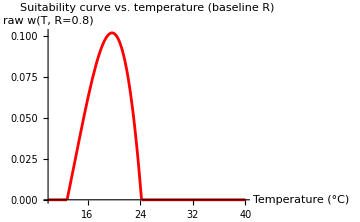

```mathematica
Rbaseline = 0.8;          (* = 0.8 by default *)
(* temperature range to sweep *)
Tmin = 10;  Tmax = 40;
suitParamsTest = <|
  "optT" -> 25, (* Optimal temperature *)
  "respBreadth" -> 150, (* Temperature response breadth *)
  "Rhalf"  -> 0.5,
  "mParams"-> {0.05, 0.1, 0.05}
|>;

wCurve = Plot[
  SuitabilityFunc[T, Rbaseline, suitParamsTest],
  {T, Tmin, Tmax},
  PlotRange   -> All,
  PlotStyle -> Red,
  AxesLabel   -> {"Temperature (°C)", "raw w(T, R=0.8)"},
  PlotLabel   -> "Suitability curve vs. temperature (baseline R)",
  PlotStyle   -> Thick,
  ImageSize   -> Medium
]
```

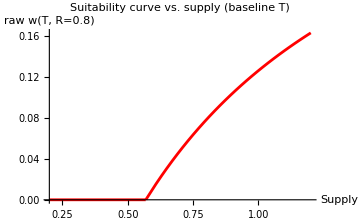

```mathematica
Tbaseline = 22;
(* supply range to sweep *)
Rmin = 0.2;  Rmax = 1.2;
suitParamsTest = <|
  "optT" -> 25, (* Optimal temperature *)
  "respBreadth" -> 150, (* Temperature response breadth *)
  "Rhalf"  -> 0.5,
  "mParams"-> {0.05, 0.1, 0.05}
|>;

wCurve = Plot[
  SuitabilityFunc[Tbaseline, R, suitParamsTest],
  {R, Rmin, Rmax},
  PlotRange   -> All,
  PlotStyle -> Red,
  AxesLabel   -> {"Supply", "raw w(T, R=0.8)"},
  PlotLabel   -> "Suitability curve vs. supply (baseline T)",
  PlotStyle   -> Thick,
  ImageSize   -> Medium
]
```

## Plot the variation in the phi result as variation in just one parameter changes

### Plot variation in varT and phi

These are the parameters that won’t change for now:

```mathematica
(* fixed params *)
epsF = 1;
suitParams = <|
  "optT"      -> 25,
  "respBreadth" -> 150,
  "Rhalf"     -> 0.5,
  "mParams"   -> {0.05, 0.1, 0.05}
|>;
nPatches = 1000;
totalS = 1000;
```

Vary only variation in T to see what happens

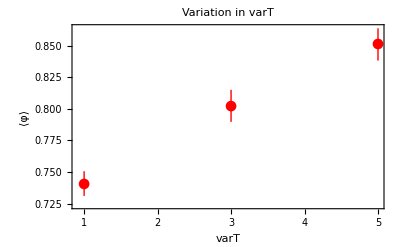

```mathematica
varTList = {1, 3, 5};
meanRList = {0.8};
varRList = {0.2};
meanTList = {22};
(* build a flat list of all 4‑tuples *)
(*paramTuples = Tuples[{meanTList, varTList, meanRList, varRList}];*)
nReps = 500;

stats = ParallelTable[
  Module[{phis, q},
    (* do nReps draws of φ at this particular (meanT,varT,meanR,varR) *)
    phis = Table[phiLandscape[ meanT, varT, meanR, varR ], {nReps}];
    q = Quantile[phis, {0.025, 0.975}];
    {varT, Mean[phis], ErrorBar[{ Mean[phis] - q[[1]],q[[2]] - Mean[phis] }]}
  ],
  {meanT, meanTList},   (* iterator 1 *)
  {varT,  varTList},    (* iterator 2 *)
  {meanR, meanRList},   (* iterator 3 *)
  {varR,  varRList}     (* iterator 4 *)
];

flatStats = Flatten[stats, 3];
statsPartitioned = Partition[flatStats, 3];

(* collect for the around thing *)
statsAround = statsPartitioned /. {x_, y_, ErrorBar[{dn_, up_}]} :> 
	{x, Around[y, {dn, up}]};

(* — now just plot — *)
ListPlot[
  statsAround,
  PlotMarkers -> Automatic,
  PlotStyle -> Red,
  Frame -> True,
  FrameLabel -> {"varT", "⟨φ⟩"},
  PlotLabel -> "Variation in varT", 
  PlotRange -> All
]
```

### Plot variation as meanT changes

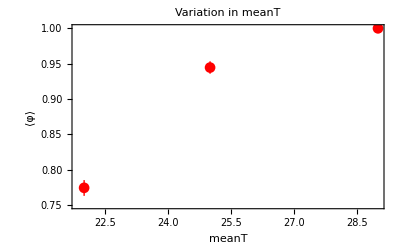

```mathematica
varTList = {2};
meanRList = {0.8};
varRList = {0.2};
meanTList = {22, 25, 29};
(* build a flat list of all 4‑tuples *)
(*paramTuples = Tuples[{meanTList, varTList, meanRList, varRList}];*)
nReps = 500;

stats = ParallelTable[
  Module[{phis, q},
    (* do nReps draws of φ at this particular (meanT,varT,meanR,varR) *)
    phis = Table[phiLandscape[ meanT, varT, meanR, varR ], {nReps}];
    q = Quantile[phis, {0.025, 0.975}];
    {meanT, Mean[phis], ErrorBar[{ Mean[phis] - q[[1]],q[[2]] - Mean[phis] }]}
  ],
  {meanT, meanTList},   (* iterator 1 *)
  {varT,  varTList},    (* iterator 2 *)
  {meanR, meanRList},   (* iterator 3 *)
  {varR,  varRList}     (* iterator 4 *)
];

flatStats = Flatten[stats, 3];
statsPartitioned = Partition[flatStats, 3];

(* collect for the around thing *)
statsAround = statsPartitioned /. {x_, y_, ErrorBar[{dn_, up_}]} :> 
	{x, Around[y, {dn, up}]};

(* — now just plot — *)
ListPlot[
  statsAround,
  PlotMarkers -> Automatic,
  PlotStyle -> Red,   
  Frame -> True,
  FrameLabel -> {"meanT", "⟨φ⟩"},
  PlotLabel -> "Variation in meanT", 
  PlotRange -> All
]
```

### Plot variation as varR changes

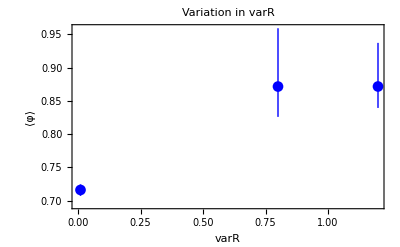

```mathematica
varTList = {2};
meanRList = {0.8};
varRList = {0.01, 0.8, 1.2};
meanTList = {22};
(* build a flat list of all 4‑tuples *)
(*paramTuples = Tuples[{meanTList, varTList, meanRList, varRList}];*)
nReps = 500;

stats = ParallelTable[
  Module[{phis, q},
    (* do nReps draws of φ at this particular (meanT,varT,meanR,varR) *)
    phis = Table[phiLandscape[ meanT, varT, meanR, varR ], {nReps}];
    q = Quantile[phis, {0.025, 0.975}];
    {varR, Mean[phis], ErrorBar[{ Mean[phis] - q[[1]],q[[2]] - Mean[phis] }]}
  ],
  {meanT, meanTList},   (* iterator 1 *)
  {varT,  varTList},    (* iterator 2 *)
  {meanR, meanRList},   (* iterator 3 *)
  {varR,  varRList}     (* iterator 4 *)
];

flatStats = Flatten[stats, 3];
statsPartitioned = Partition[flatStats, 3];

(* collect for the around thing *)
statsAround = statsPartitioned /. {x_, y_, ErrorBar[{dn_, up_}]} :> 
	{x, Around[y, {dn, up}]};

(* — now just plot — *)
ListPlot[
  statsAround,
  PlotMarkers -> Automatic,
  PlotStyle -> Blue,        
  Frame -> True,
  FrameLabel -> {"varR", "⟨φ⟩"},
  PlotLabel -> "Variation in varR", 
  PlotRange -> All
]
```

### Plot variation as meanR changes

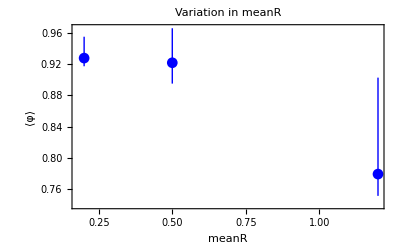

```mathematica
varTList = {2};
meanRList = {0.2, 0.5, 1.2};
varRList = {0.8};
meanTList = {22};
(* build a flat list of all 4‑tuples *)
(*paramTuples = Tuples[{meanTList, varTList, meanRList, varRList}];*)
nReps = 500;

stats = ParallelTable[
  Module[{phis, q},
    (* do nReps draws of φ at this particular (meanT,varT,meanR,varR) *)
    phis = Table[phiLandscape[ meanT, varT, meanR, varR ], {nReps}];
    q = Quantile[phis, {0.025, 0.975}];
    {meanR, Mean[phis], ErrorBar[{ Mean[phis] - q[[1]],q[[2]] - Mean[phis] }]}
  ],
  {meanT, meanTList},   (* iterator 1 *)
  {varT,  varTList},    (* iterator 2 *)
  {meanR, meanRList},   (* iterator 3 *)
  {varR,  varRList}     (* iterator 4 *)
];

flatStats = Flatten[stats, 3];
statsPartitioned = Partition[flatStats, 3];

(* collect for the around thing *)
statsAround = statsPartitioned /. {x_, y_, ErrorBar[{dn_, up_}]} :> 
	{x, Around[y, {dn, up}]};

(* — now just plot — *)
ListPlot[
  statsAround,
  PlotMarkers -> Automatic,
  PlotStyle -> Blue,        
  Frame -> True,
  FrameLabel -> {"meanR", "⟨φ⟩"},
  PlotLabel -> "Variation in meanR", 
  PlotRange -> All
]
```

## Plot variation in two variables with phi

### Start with variation in both R directions

```mathematica
meanTList = {22};
varTList  = {2};
meanRList = {0.2, 0.4, 0.6, 0.8, 1.0, 1.2};
varRList  = {0.2, 0.4, 0.6, 0.8, 1.0, 1.2}; 
nReps     = 500;

phiMeans4D = ParallelTable[
  Module[{phis},
    phis = Table[
      phiLandscape[meanT, varT, meanR, varR],
      {nReps}
    ];
    Mean[phis]
  ],
  {meanT, meanTList},
  {varT,  varTList},
  {meanR, meanRList},
  {varR,  varRList}
];
phiGrid = phiMeans4D[[1, 1, All, All]]; (* this gets changed accordingly*)
ListPlot3D[
  phiGrid,
  DataRange -> {{First@meanRList, Last@meanRList},
               {First@varRList, Last@varRList}},
  AxesLabel -> {"meanR", "varR", "⟨ϕ⟩"},
  PlotRange -> All,
  Mesh -> None,
  ColorFunction -> "Temperature", 
  PlotLabel   -> "φ over meanR, varR"
]
```

-Graphics3D-

### Variation in both of the variation directions

```mathematica
meanTList = {22};
varTList  = {1, 2, 3, 4, 5, 6};
meanRList = {0.8};
varRList  = Subdivide[0.01, 1.2, 5]; 
nReps     = 500;

phiMeans4D = ParallelTable[
  Module[{phis},
    phis = Table[
      phiLandscape[meanT, varT, meanR, varR],
      {nReps}
    ];
    Mean[phis]
  ],
  {meanT, meanTList},
  {varT,  varTList},
  {meanR, meanRList},
  {varR,  varRList}
];
phiGrid = phiMeans4D[[1, All, 1, All]];
ListPlot3D[
  phiGrid,
  DataRange -> {{First@varTList, Last@varTList},
               {First@varRList, Last@varRList}},
  AxesLabel -> {"varT", "varR", "⟨ϕ⟩"},
  PlotRange -> All,
  Mesh -> None,
  ColorFunction -> "Temperature", 
  PlotLabel   -> "φ over varT, varR"
]
```

-Graphics3D-

### Variation in both of the temperature directions

```mathematica
meanTList = {20, 22, 24, 26, 28, 30};
varTList  = {1, 2, 3, 4, 5, 6};
meanRList = {0.8};
varRList  = {0.2}; 
nReps     = 500;

phiMeans4D = ParallelTable[
  Module[{phis},
    phis = Table[
      phiLandscape[meanT, varT, meanR, varR],
      {nReps}
    ];
    Mean[phis]
  ],
  {meanT, meanTList},
  {varT,  varTList},
  {meanR, meanRList},
  {varR,  varRList}
];
phiGrid = phiMeans4D[[All, All, 1, 1]];
ListPlot3D[
  phiGrid,
  DataRange -> {{First@meanTList, Last@meanTList},
               {First@varTList, Last@varTList}},
  AxesLabel -> {"meanT", "varT", "⟨ϕ⟩"},
  PlotRange -> All,
  Mesh -> None,
  ColorFunction -> "Temperature", 
  PlotLabel   -> "φ over temperature"
]
```

-Graphics3D-

### Variation in both of the supply (R) directions

```mathematica
meanTList = {22};
varTList  = {2};
meanRList = {0.2, 0.4, 0.6, 0.8, 1.0, 1.2};
varRList  = Subdivide[0.01, 1.2, 5]; 
nReps     = 500;

phiMeans4D = ParallelTable[
  Module[{phis},
    phis = Table[
      phiLandscape[meanT, varT, meanR, varR],
      {nReps}
    ];
    Mean[phis]
  ],
  {meanT, meanTList},
  {varT,  varTList},
  {meanR, meanRList},
  {varR,  varRList}
];
phiGrid = phiMeans4D[[1, 1, All, All]];
ListPlot3D[
  phiGrid,
  DataRange -> {{First@meanRList, Last@meanRList},
               {First@varRList, Last@varRList}},
  AxesLabel -> {"meanR", "varR", "⟨ϕ⟩"},
  PlotRange -> All,
  Mesh -> None,
  ColorFunction -> "Temperature", 
  PlotLabel   -> "φ over supply"
]
```

-Graphics3D-